```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v3/phase/Tc240alphap30/exam/BUFFER

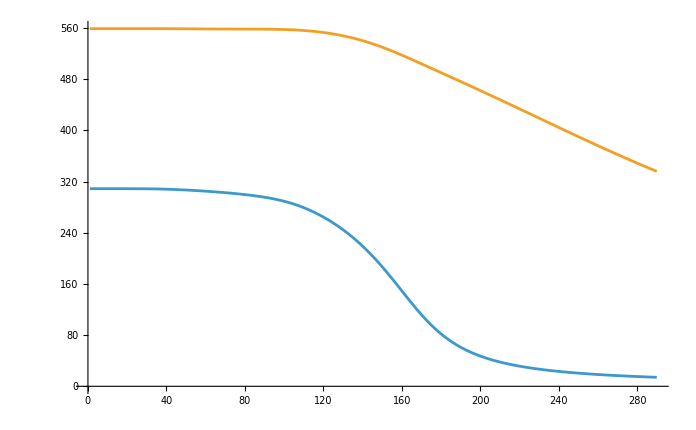

```mathematica
mf=Transpose[Import["./MF.DAT"]][[1]];
mfs=Transpose[Import["./MF.DAT"]][[2]];
ListLinePlot[{mf,mfs}]
```

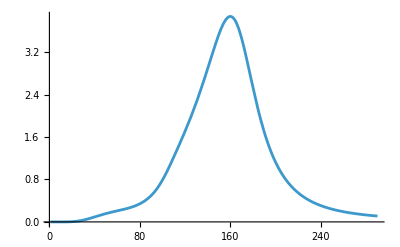

```mathematica
intmf=Interpolation[mf];
dmdt=D[intmf[x],x];
Plot[-dmdt,{x,1,Length[mf]}]
```

```mathematica
FindMaximum[-dmdt,{x,140}]
```

InterpolatingFunction::dmval: 输入值 {-1452.98} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {-59.4088} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

{3.87072,{x→159.925}}